```mathematica
Hdg1=ParallelTable[{x,InHf2qD[x,0.1,-1]},{x,Join[Range[0.1,0.3,0.001],Range[0.31,0.5,0.01],Range[0.51,1,0.05]]}];
```

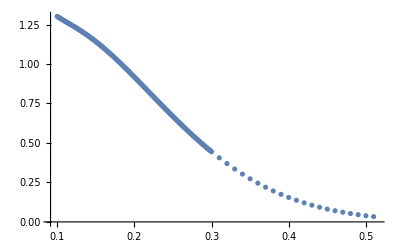

```mathematica
ListPlot[Hdg1]
```

```mathematica
Hdg1[[206]]
```

{0.35,0.272927}

```mathematica
ap1=(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
ap0=(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
```

```mathematica
0.5*0.05888785346404517
```

0.0294439

```mathematica
ap0/ap1
```

0.25

```mathematica
Hdgf1=Interpolation[Hdg1];
Hdgre1[x_]=ap1*Hdgf1[x]+ap0*Hdgf1[x]
```

0.0368049 InterpolatingFunction[…][x]

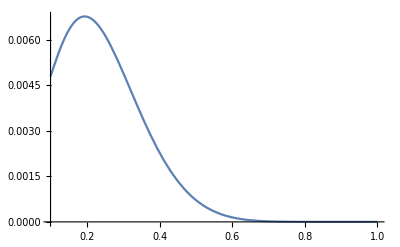

```mathematica
Plot[x*Hdgre1[x],{x,0.1,1}]
```

```mathematica
Her1=ParallelTable[{x,InHf2q[x,ξc,-1]},{x,-0.1,0.1,0.001}];
Hda1=ParallelTable[{x,InAf1[x,ξc,-1]},{x,-0.1,0.1,0.001}];
```

$Aborted

$Aborted

```mathematica
InHf2qD[0.1,ξc,-1]
```

1.30128